```mathematica
lines=ReadList["!ngspice -b "<>NotebookDirectory[]<>"thing.net",String];
```

```mathematica
fullOutput=StringJoin[StringJoin[#,"\n"]&/@lines];
```

```mathematica
splitOutput=StringSplit[fullOutput,"--------------------------------------------------------------------------------"];
```

```mathematica
stringdata=StringDrop[#,-(StringLength[#]-StringPosition[#,"\f"]⟦1,1⟧+3)]&/@splitOutput⟦3;;Length[splitOutput]-1⟧;
stringdata=Append[stringdata,StringDrop[splitOutput⟦Length[splitOutput]⟧,-(StringLength[splitOutput⟦Length[splitOutput]⟧]-StringPosition[splitOutput⟦Length[splitOutput]⟧,"CPU"]⟦1,1⟧+2)]];
```

```mathematica
data=Flatten[(ImportString[#,"Table"]⟦2;;⟧&/@stringdata),1];
data=#⟦2;;⟧&/@data;
```

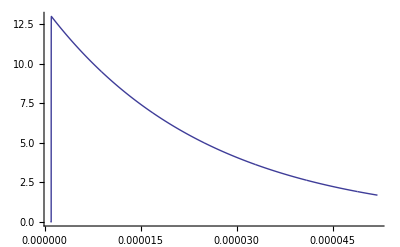

```mathematica
ListPlot[data,Joined->True,PlotStyle->Thick]
```

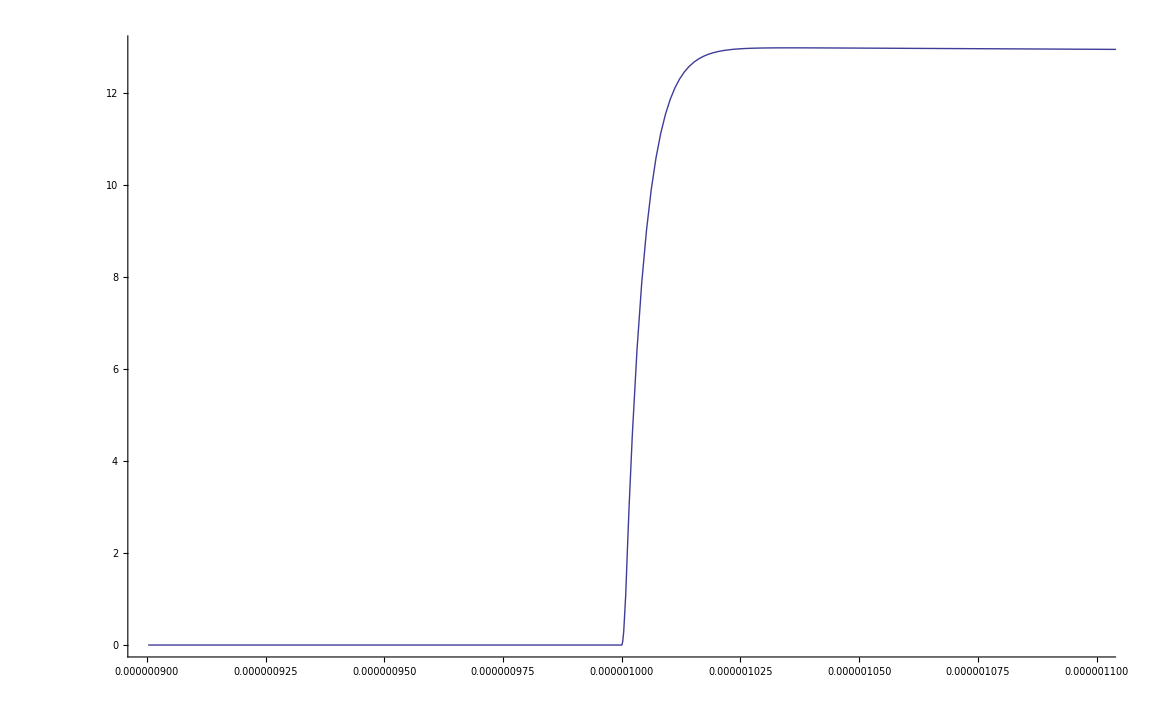

```mathematica
ListPlot[data,Joined->True,PlotRange->{{.9×10^-6,1.1×10^-6},Automatic},PlotStyle->Thick]
```